```mathematica
SetDirectory["D:\\Qsync\\QOLab\\Data\\On Resonance Project\\Lab Book 2 (18 Mar 29 -)\\20-09-28\\Power\\85F12"];
data=Import[#]&/@FileNames["*csv"];
data2=Table[Take[data[[i]],{17,-2}],{i,1,Length[data]}];
SetDirectory["D:\\Qsync\\QOLab\\Data\\On Resonance Project\\Lab Book 2 (18 Mar 29 -)\\20-09-28\\Power\\85F12\\Off"];
dataoff=Import[#]&/@FileNames["*csv"];
data2off=Table[Take[dataoff[[i]],{17,-2}],{i,1,Length[dataoff]}];
```

```mathematica
f[data_]:=Module[{ll,max,min,yaxis1,yaxis2,wcn,ff,gg,loc,kk},
ll=data[[All,2]];
{max,min}=#[ll]&/@{Max,Min};
yaxis1=Take[data[[All,4]],Flatten[{#[ll,min][[1]],#[ll,max][[-1]]}&@Position]];
yaxis2=Take[data[[All,8]],Flatten[{#[ll,min][[1]],#[ll,max][[-1]]}&@Position]];

wcn=(794.76728224*10^-9);


ff[x_]:=Evaluate[Fit[


Flatten[{Table[{o,yaxis1[[o]]},{o,10,200}],Table[{o,yaxis1[[o]]},{o,Length[yaxis1]-200,Length[yaxis1]-10}]},1]

,{1,x},x]];
gg=Table[ff[x],{x,1,Length[yaxis1]}];
loc=Select[FindPeaks[
GaussianFilter[yaxis2,10]
,16,0.00002],1500<#[[1]]<4500&];
kk[x_]:=Evaluate[Fit[{{loc[[1,1]],-0.361},{loc[[-1,1]],-0.361/2}},{1,x},x]];
{-12.531885282826405 wcn Log[yaxis1/gg],GaussianFilter[yaxis1/gg,5],yaxis2,Table[kk[x],{x,1,Length[yaxis1]}]}

]
```

```mathematica
Manipulate[
ListPlot[{GaussianFilter[data2[[i]][[All,8]],10],
Select[FindPeaks[
GaussianFilter[data2[[i]][[All,8]],10]
,16,0.00002],1500<#[[1]]<4500&]},PlotStyle->{Black,{Red,AbsolutePointSize[5]}}]
,{{i,62},1,Length[data2],1}]
```

```mathematica
Manipulate[ListPlot[Transpose[f[data2[[i]]][[{4,2}]]],PlotRange->{{-0.010+0.361,0.05+0.361},{0.6,0.85}},Joined->True,Epilog->Line[{{-2,1},{2,1}}]],{{i,2},1,Length[data2],1}]
```

```mathematica
power[[49]]
```

20

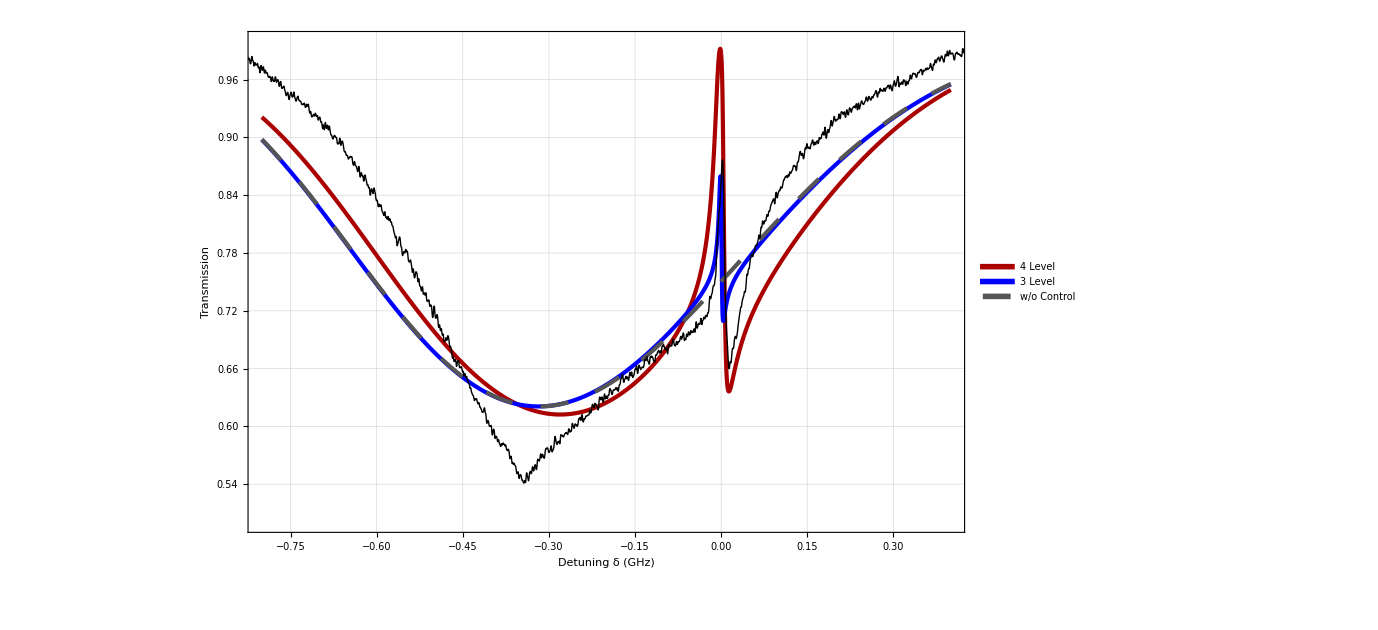

```mathematica
final2=ListPlot[{Lev4DoppTestsc[23,15/1000,0.9/1000,1.438*10^6,0*10^6,0],Lev3DoppTestsc[23,15/1000,0.9/1000,1.438*10^6,0*10^6,0],Lev3DoppTestsc[23,0/1000,1/1000,0.5*10^6,0*10^6,0]},Joined->True,FrameTicks->True,FrameTicksStyle->Directive[40],Frame->True,Axes->False,PlotLegends->Placed[legend,{Right,Bottom}],ImageSize->1020,PlotStyle-> {{AbsoluteThickness[3],Darker[Red]},{AbsoluteThickness[3],Blue},{AbsoluteThickness[3],Darker[Gray],Dashing[.02]},{AbsoluteThickness[3],Black,Dashed}},FrameLabel->{Style["Detuning δ (GHz)",50,Black],Style["Transmission ",50,Black]},GridLines->Automatic,PlotRange->{{-0.8,0.4},{0.5,1.0}}];
Show[final2,ListPlot[Transpose[f[data2[[45]]][[{4,2}]]],Joined->True,PlotStyle->{Thick,Black},Epilog->Line[{{-2,1},{2,1}}]]]
```

```mathematica
Lev3DoppTestsc[T_,P_,diam_,gam_,delt_,ab_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,Ωc1,Ωc2,Δ2,d31,d41},
d=Range[-0.8,0.4,0.0001]*10^9;
Δ2=2Pi d;(*Raman detuning*)
Δ=2Pi delt;
δ=Δ2-Δ;
Nat=Rbpress[T][[1]];
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d31=Sqrt[5/27]*2.537717 10^-29;
d41=Sqrt[4/27]*2.537717 10^-29;
d32=Sqrt[2/27]*2.537717 10^-29;
d42=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi(361*10^6) ;
u=Rbpress[T][[4]]; 

omegac1=(1/ℏ Sqrt[1/(e0 c)]*d32*Sqrt[P/(Pi*(diam/2)^2)]); 


Ωc1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
Ωc2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 
If[ab==0,
(*{Transpose[{d/10^9,Im[sd3e[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]}],
Transpose[{d/10^9,Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]}],
Transpose[{d/10^9,Im[sd3e[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]]}],
Transpose[{d/10^9,Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]]}]
}*)Transpose[{d/10^9,
Exp[-2Pi*0.0254*3/(2wcn)(Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]+Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]])]}],

(*Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]+Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]])]}]*)
If[ab==3,
Transpose[{d/10^9,
(Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]]+Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]])}],
{
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd3a[wc,γ21,γ32,δ,Δ+w43,Ωc2,c,ℏ,e0,u,Nat,d42]])]}],
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd3a[wc,γ21,γ32,δ,Δ,Ωc1,c,ℏ,e0,u,Nat,d32]])]
}]
}
]]]
```

```mathematica
Lev4DoppTestsc[T_,P_,diam_,gam_,delt_,ab_] :=
Module[{Nat,γ32,omegac1,omegac2,c,e0,ℏ,f,χ42,χ32,χ24,χ23,w43,Δ,d32,d42,γ42,wcn,α1,α2,β1,β2,Zα,Zβ,dopp,u,wc,d,δ,γ21,αα1,αα2,Zαα,ββ1,ββ2,Zββ,fI,Δ2,d31,d41},
d=Range[-0.8,0.4,0.0001]*10^9;
Δ2=2Pi d;(*Raman detuning*)
Δ=2Pi delt;
δ=Δ2-Δ;
Nat=Rbpress[T][[1]];
γ21=2Pi gam;
γ32=2*Pi*5.750056 10^6/2;
γ42=2*Pi*5.750056 10^6/2;
(*γ32=γ21/0.035;*)
d31=Sqrt[5/27]*2.537717 10^-29;
d41=Sqrt[4/27]*2.537717 10^-29;
d32=Sqrt[2/27]*2.537717 10^-29;
d42=Sqrt[7/27]*2.537717 10^-29;
ℏ=1.0546 10^-34;
e0=8.8542 10^-12;
c=2.9979 10^8;
wcn=(794.76728224*10^-9);
wc=2Pi 377.107385*10^12;
w43=2Pi(316*10^6) ;
u=Rbpress[T][[4]]; 

omegac1=(1/ℏ Sqrt[1/(e0 c)]*d31*Sqrt[P/(Pi*(diam/2)^2)]); 
omegac2=(1/ℏ Sqrt[1/(e0 c)]*d41*Sqrt[P/(Pi*(diam/2)^2)]); 

If[ab==0,
(*{Transpose[{d/10^9,Im[sd24[wc,γ21,γ42,γ32,δ,Δ,omegac2,c,ℏ,e0,u,Nat,w43,d42]]}],
Transpose[{d/10^9,Im[sd42[wc,γ21,γ42,γ32,δ,Δ,omegac2,c,ℏ,e0,u,Nat,w43,d42]]}],
Transpose[{d/10^9,Im[sd23[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]]}],
Transpose[{d/10^9,Im[sd32[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]]}]
}*)
Transpose[{d/10^9,
Exp[-2Pi*0.0254*3/(2wcn)(Im[sd42[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d42]]+Im[sd32[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]])]
}]

,
(*Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd42[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d42]]+Im[sd32[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]])]
}]*)
If[ab==3,
{Transpose[{d/10^9,
Im[sd32[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]]
}],
Transpose[{d/10^9,
Im[sd42[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d42]]
}]},
{Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd32[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d32]])]
}],
Transpose[{d/10^9,
Exp[-2Pi*0.0254/(2wcn)(Im[sd42[wc,γ21,γ42,γ32,δ,Δ,omegac1,c,ℏ,e0,u,Nat,w43,d42]])]
}]}
]]
]
```

```mathematica
Manipulate[
lc=FindPeaks[Select[Transpose[f[data2[[i]]][[{4,2}]]],-0.02+0.361<#[[1]]<0.05+0.361&][[All,2]],10,0.00005];
kk=Select[Transpose[f[data2[[i]]][[{4,2}]]],-0.02+0.361<#[[1]]<0.05+0.361&][[lc[[All,1]]]];
ListPlot[
{Transpose[f[data2[[i]]][[{4,2}]]],kk}
,PlotRange->{{-0.02+0.361,0.05+0.361},{0.5,1}}
,ImageSize->1000,PlotStyle->{Blue,{AbsolutePointSize[5],Red}},Joined->{True,False},Epilog->Line[{{-2,1},{2,1}}]],{{i,2},1,Length[data2],1}]
```

ListPlot::lpn: {{{-0.391467,1.00264},{-0.39129,1.00312},{-0.391113,1.00349},{-0.390936,1.00362},{-0.390759,1.00347},{-0.390581,1.00308},{-0.390404,1.00259},{-0.390227,1.00215},{-0.39005,1.0016},«33»,{-0.384027,1.00071},{-0.38385,1.00057},{-0.383673,1.00061},{-0.383496,1.00098},{-0.383319,1.00115},{-0.383142,1.00137},{-0.382965,1.00126},{-0.382788,1.00088},«6192»},{}} is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

ListPlot::lpn: {{{-1.47337,1.00111},{-1.47279,1.00205},{-1.4722,0.997074},{-1.47161,0.998491},{-1.47102,1.00102},{-1.47044,1.00396},{-1.46985,1.00146},{-1.46926,0.999918},{-1.46867,0.999895},«33»,{-1.4487,1.00112},{-1.44811,1.00157},{-1.44752,1.00506},{-1.44694,1.00456},{-1.44635,0.999509},{-1.44576,0.996053},{-1.44517,0.998505},{-1.44459,0.993533},«6199»},{}} is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

ListPlot::lpn: {{{-0.917187,1.00011},{-0.916893,1.00011},{-0.916599,1.00015},{-0.916306,1.00032},{-0.916012,1.00057},{-0.915718,1.00095},{-0.915424,1.00112},{-0.915131,1.00109},{-0.914837,1.00086},«33»,{-0.90485,1.00309},{-0.904556,1.00271},{-0.904262,1.00204},{-0.903969,1.00102},{-0.903675,0.999843},{-0.903381,0.998192},{-0.903087,0.996804},{-0.902794,0.995666},«6199»},{}} is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

ListPlot::lpn: {{{-1.09769,1.00011},{-1.09739,1.00011},{-1.0971,1.00015},{-1.09681,1.00032},{-1.09651,1.00057},{-1.09622,1.00095},{-1.09592,1.00112},{-1.09563,1.00109},{-1.09534,1.00086},«33»,{-1.08535,1.00309},{-1.08506,1.00271},{-1.08476,1.00204},{-1.08447,1.00102},{-1.08417,0.999843},{-1.08388,0.998192},{-1.08359,0.996804},{-1.08329,0.995666},«6199»},{}} is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

ListPlot::lpn: {{{-1.10469,0.978683},{-1.10437,0.981736},{-1.10405,0.984796},{-1.10373,0.987898},{-1.10341,0.990836},{-1.10309,0.993529},{-1.10277,0.995762},{-1.10245,0.99792},{-1.10213,0.999485},«33»,{-1.09129,1.00035},{-1.09097,1.0002},{-1.09065,1.00007},{-1.09033,1.00005},{-1.09002,0.999873},{-1.0897,0.999949},{-1.08938,0.999909},{-1.08906,1.00001},«6200»},{}} is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

```mathematica
Manipulate[
ListPlot[{Select[Transpose[f[data2[[i]]][[{4,2}]]],-0.02<#[[1]]<0.05&][[All,2]],FindPeaks[Select[Transpose[f[data2[[i]]][[{4,2}]]],-0.02<#[[1]]<0.05&][[All,2]],10,0.00005]},PlotStyle->{Blue,{AbsolutePointSize[8],Red}}]
,{i,1,Length[data2],1}]
```

```mathematica
EITmax7712=Table[
lc=FindPeaks[Select[Transpose[f[data2[[i]]][[{4,2}]]],-0.02<#[[1]]<0.05&][[All,2]],10,0.00005];
Select[Transpose[f[data2[[i]]][[{4,2}]]],-0.02<#[[1]]<0.05&][[lc[[All,1]]]][[1,2]]
,{i,1,Length[data2]}]
```

{0.844239,0.839966,0.843375,0.834647,0.835956,0.831161,0.842169,0.799155,0.809581,0.817416,0.816427,0.828086,0.827615,0.822377,0.819082,0.821829,0.835297,0.833118,0.8308,0.835287,0.836823,0.840031,0.835987,0.838163,0.839659,0.855989,0.844331,0.841706,0.849182,0.835507,0.85068,0.845239,0.853183,0.855299,0.851959,0.854181,0.854941,0.85613,0.856676,0.857037,0.865048,0.862734,0.857725,0.868049,0.876787,0.873029,0.874902,0.870861,0.875953,0.874476,0.873023,0.8797,0.892576,0.886116,0.885724,0.884357,0.889097,0.879191,0.883649,0.883946,0.886362,0.888006,0.886704,0.889462,0.894939,0.890324,0.893904,0.896007,0.897517,0.898532,0.899094,0.897424,0.891846,0.89618,0.903218,0.902495,0.903575,0.903977,0.904634,0.898265,0.900709,0.907314,0.906814,0.90837}

```mathematica
EITmin7712=Table[
Select[Transpose[f[data2[[i]]][[{4,2}]]],-0.02<#[[1]]<0.05&][[All,2]]//Min
,{i,1,Length[data2]}]
```

{0.806025,0.797376,0.801422,0.797113,0.778849,0.790215,0.784907,0.743634,0.73107,0.733906,0.733891,0.731076,0.722402,0.720944,0.722976,0.728475,0.712797,0.71528,0.714802,0.710363,0.702161,0.702445,0.702774,0.706979,0.690435,0.702212,0.691588,0.69822,0.689729,0.684108,0.692143,0.690671,0.685552,0.683272,0.68933,0.691194,0.680487,0.682182,0.68378,0.687327,0.679058,0.672754,0.675957,0.673593,0.659925,0.656981,0.660438,0.659955,0.638704,0.635684,0.633066,0.639266,0.631342,0.629428,0.627636,0.628596,0.622363,0.621429,0.618711,0.617538,0.613501,0.613526,0.606454,0.608214,0.602922,0.600961,0.603516,0.609514,0.594138,0.594219,0.588114,0.594142,0.589195,0.589245,0.596304,0.589979,0.579158,0.578136,0.582221,0.582446,0.579178,0.58182,0.578976,0.579774}

```mathematica
pw={0.5,1,2,3,4,5,6,7,8,9,10,15,20,25,30,35,40,50,60,70,80};power=Flatten[Transpose[{pw,pw,pw,pw}]];
```

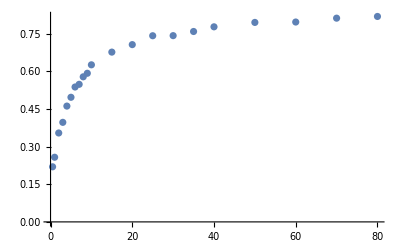

```mathematica
rb8512=ListPlot[{Transpose[{pw,1-Log[Mean/@Partition[EITmax7712,4]]/Log[Mean/@Partition[EITmin7712,4]]}]}]
```

```mathematica
Table[Select[Transpose[f[data2off[[1]]][[{4,2}]]],-0.02+0.361<#[[1]]<0.02+0.361&][[All,2]]//Min,{i,1,Length[dataoff],1}]//Mean
```

0.763575

```mathematica
halfv7712=EITmin7712+(EITmax7712-EITmin7712)/2
```

{0.825132,0.818671,0.822399,0.81588,0.807402,0.810688,0.813538,0.771395,0.770326,0.775661,0.775159,0.779581,0.775008,0.771661,0.771029,0.775152,0.774047,0.774199,0.772801,0.772825,0.769492,0.771238,0.769381,0.772571,0.765047,0.779101,0.767959,0.769963,0.769456,0.759808,0.771412,0.767955,0.769368,0.769286,0.770645,0.772688,0.767714,0.769156,0.770228,0.772182,0.772053,0.767744,0.766841,0.770821,0.768356,0.765005,0.76767,0.765408,0.757328,0.75508,0.753044,0.759483,0.761959,0.757772,0.75668,0.756477,0.75573,0.75031,0.75118,0.750742,0.749932,0.750766,0.746579,0.748838,0.74893,0.745642,0.74871,0.75276,0.745827,0.746376,0.743604,0.745783,0.740521,0.742713,0.749761,0.746237,0.741366,0.741057,0.743427,0.740355,0.739944,0.744567,0.742895,0.744072}

```mathematica
Manipulate[
Which[i≤1,
ddd=Select[Transpose[f[data2[[i]]][[{4,2}]]],0.03<#[[1]]<0.046&];,
2≥ i>1,
ddd=Select[Transpose[f[data2[[i]]][[{4,2}]]],0.02<#[[1]]<0.035&];,
3≥ i>2,
ddd=Select[Transpose[f[data2[[i]]][[{4,2}]]],0.015<#[[1]]<0.03&];,
4≥ i>3∨i==7,
ddd=Select[Transpose[f[data2[[i]]][[{4,2}]]],0.03<#[[1]]<0.05&];,
5≥ i>4,
ddd=Select[Transpose[f[data2[[i]]][[{4,2}]]],0.02<#[[1]]<0.035&];,
6≥ i>5,
ddd=Select[Transpose[f[data2[[i]]][[{4,2}]]],0.01<#[[1]]<0.03&];,
9≥  i>6,
ddd=Select[Transpose[f[data2[[i]]][[{4,2}]]],-0.02<#[[1]]<0.01&];,
19 >= i>9∨i==26∨i==21,
ddd=Select[Transpose[f[data2[[i]]][[{4,2}]]],-0.02<#[[1]]<0.02&];,
29≥   i>19,
ddd=Select[Transpose[f[data2[[i]]][[{4,2}]]],-0.03<#[[1]]<0.01&];,
   i==63∨i==65∨i==74∨i==76∨i==77∨i==79∨i==80∨i==81∨i==82∨i==83∨i==84,
ddd=Select[Transpose[f[data2[[i]]][[{4,2}]]],-0.05<#[[1]]<0.024&]; ,
  i>29,
ddd=Select[Transpose[f[data2[[i]]][[{4,2}]]],-0.03<#[[1]]<0.024&];


];
Nearest[ddd[[All,2]],halfv7712[[i]],4];
pos=Position[ddd[[All,2]],#]&/@Nearest[ddd[[All,2]],halfv7712[[i]],If[i==51∨i==58∨i==63∨i==67∨i==70∨i==75∨i==76∨i==81,18,5]];
ddd1=ddd[[Sort[Flatten[pos]]]];
f1=Evaluate[Fit[ddd1[[{1,2}]],{1,x},x]];
f2=Evaluate[Fit[ddd1[[{-1,-2}]],{1,x},x]];
Show[ListPlot[{ddd,ddd1},PlotStyle->{Black,{Blue,AbsolutePointSize[8]}},Epilog->Line[{{-1,halfv7712[[i]]},{1,halfv7712[[i]]}}]],Plot[{f1,f2},{x,-2,1},PlotRange->{0,1},PlotStyle->{{Red,Dashed},{Red,Dashed}}]]
,{i,1,Length[data2],1}]
Abs[Solve[f1==halfv7712[[1]],x][[1,1,2]]-Solve[f2==halfv7712[[1]],x][[1,1,2]]]*10^3(*in MHz*)
```

2.08571

```mathematica
fff={};
Do[
Which[i≤1,
ddd=Select[Transpose[f[data2[[i]]][[{4,2}]]],0.03<#[[1]]<0.046&];,
2≥ i>1,
ddd=Select[Transpose[f[data2[[i]]][[{4,2}]]],0.02<#[[1]]<0.035&];,
3≥ i>2,
ddd=Select[Transpose[f[data2[[i]]][[{4,2}]]],0.015<#[[1]]<0.03&];,
4≥ i>3∨i==7,
ddd=Select[Transpose[f[data2[[i]]][[{4,2}]]],0.03<#[[1]]<0.05&];,
5≥ i>4,
ddd=Select[Transpose[f[data2[[i]]][[{4,2}]]],0.02<#[[1]]<0.035&];,
6≥ i>5,
ddd=Select[Transpose[f[data2[[i]]][[{4,2}]]],0.01<#[[1]]<0.03&];,
9≥  i>6,
ddd=Select[Transpose[f[data2[[i]]][[{4,2}]]],-0.02<#[[1]]<0.01&];,
19 >= i>9∨i==26∨i==21,
ddd=Select[Transpose[f[data2[[i]]][[{4,2}]]],-0.02<#[[1]]<0.02&];,
29≥   i>19,
ddd=Select[Transpose[f[data2[[i]]][[{4,2}]]],-0.03<#[[1]]<0.01&];,
   i==63∨i==65∨i==74∨i==76∨i==77∨i==79∨i==80∨i==81∨i==82∨i==83∨i==84,
ddd=Select[Transpose[f[data2[[i]]][[{4,2}]]],-0.05<#[[1]]<0.024&]; ,
  i>29,
ddd=Select[Transpose[f[data2[[i]]][[{4,2}]]],-0.03<#[[1]]<0.024&];


];
Nearest[ddd[[All,2]],halfv7712[[i]],4];
pos=Position[ddd[[All,2]],#]&/@Nearest[ddd[[All,2]],halfv7712[[i]],If[i==51∨i==58∨i==63∨i==67∨i==70∨i==75∨i==76∨i==81,18,5]];
ddd1=ddd[[Sort[Flatten[pos]]]];
fff=Append[fff,ddd1];
,{i,1,Length[data2],1}]
Abs[Solve[f1==halfv7712[[1]],x][[1,1,2]]-Solve[f2==halfv7712[[1]],x][[1,1,2]]]*10^3(*in MHz*)
```

613.287

```mathematica
fff[[1]]
```

{{0.0388565,0.824477},{0.0391886,0.827307},{0.0451665,0.826343},{0.0454986,0.825133},{0.0458307,0.823864}}

```mathematica
kkk={};
Do[
cc=ClusterClassify[fff[[i]],Method->"DBSCAN"];
kkk=Append[kkk,Mean/@GatherBy[fff[[i]],cc]]
,{i,1,Length[data2],1}]
```

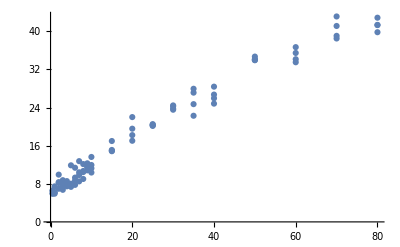

```mathematica
ListPlot[Transpose[{power,Table[Abs[kkk[[i,1,1]]-kkk[[i,2,1]]]*1000,{i,1,Length[data2],1}]}]]
```

```mathematica
Transpose[{power,Table[Abs[kkk[[i,1,1]]-kkk[[i,2,1]]]*1000,{i,1,Length[data2],1}]}]
```

{{0.5,6.47608},{0.5,6.02753},{0.5,5.89973},{0.5,6.61607},{1,6.13833},{1,5.92066},{1,7.45183},{1,6.24681},{2,6.95475},{2,9.91758},{2,8.15913},{2,8.33832},{3,8.75048},{3,8.03272},{3,6.73268},{3,7.48104},{4,7.46673},{4,8.55606},{4,7.6913},{4,7.86795},{5,11.8707},{5,7.3543},{5,7.93407},{5,8.02222},{6,9.29404},{6,11.3613},{6,7.76678},{6,8.69492},{7,9.83694},{7,12.7472},{7,10.4012},{7,8.50181},{8,10.4568},{8,12.1331},{8,9.00919},{8,10.6765},{9,11.5829},{9,11.4864},{9,10.8171},{9,12.2915},{10,11.9378},{10,10.3566},{10,13.6257},{10,11.2427},{15,14.9251},{15,16.9714},{15,15.0946},{15,14.8335},{20,17.0237},{20,21.9923},{20,19.5568},{20,18.2097},{25,20.2662},{25,20.1397},{25,20.3841},{25,20.5114},{30,24.4394},{30,24.2509},{30,23.7664},{30,23.5367},{35,24.7078},{35,27.121},{35,22.2732},{35,27.9345},{40,26.7134},{40,28.3776},{40,24.8151},{40,25.9392},{50,34.6874},{50,34.1486},{50,33.9783},{50,33.9216},{60,35.4498},{60,36.6687},{60,33.4979},{60,34.1353},{70,38.4845},{70,41.1086},{70,39.0394},{70,43.1068},{80,42.846},{80,41.2969},{80,41.3348},{80,39.8011}}

```mathematica
rb85w12={{0.5,6.476080956761776},{0.5,6.027527075812278},{0.5,5.899734982332205},{0.5,6.616071428571457},{1,6.138327205882366},{1,5.920656028368776},{1,7.451834862385355},{1,6.246812386156615},{2,6.954749103942633},{2,9.917582417582338},{2,8.15913284132841},{2,8.338315217391331},{3,8.750475285171145},{3,8.0327225130891},{3,6.73268206039072},{3,7.481040564373764},{4,7.466726618705029},{4,8.556061987237795},{4,7.691296464188591},{4,7.867948717948789},{5,11.870720720720707},{5,7.3542958370239235},{5,7.93406593406587},{5,8.022222222222265},{6,9.294037940379473},{6,11.361258865248193},{6,7.766781411359558},{6,8.69491525423734},{7,9.836937716262984},{7,12.747175141243016},{7,10.40115248226947},{7,8.501811594202971},{8,10.456773618538362},{8,12.133057090239486},{8,9.00919439579695},{8,10.676524953789235},{9,11.582887700534691},{9,11.486363636363647},{9,10.817084078711847},{9,12.29151119402977},{10,11.937830687830719},{10,10.356557377049104},{10,13.62566607460025},{10,11.242747440273037},{15,14.925064599483173},{15,16.971441124780164},{15,15.094630281690113},{15,14.833477508650494},{20,17.023691335739887},{20,21.992328519855555},{20,19.556838365896972},{20,18.209734513274345},{25,20.266155088852962},{25,20.139681208053705},{25,20.38405172413782},{25,20.511363636363576},{30,24.439380530973498},{30,24.25085034013604},{30,23.76635111876091},{30,23.536701208980993},{35,24.70778688524594},{35,27.12096774193551},{35,22.273237179487147},{35,27.93452380952388},{40,26.713409648405463},{40,28.377577319587566},{40,24.815057283142366},{40,25.939200680272112},{50,34.68739130434773},{50,34.14864864864859},{50,33.978279386711996},{50,33.9215517241378},{60,35.44982847341343},{60,36.66873963515754},{60,33.497928748964334},{60,34.13534935379645},{70,38.48453177257516},{70,41.108638743455494},{70,39.03944020356226},{70,43.10675105485229},{80,42.84595959595955},{80,41.29691516709516},{80,41.33478605388263},{80,39.80105777054516}};
```

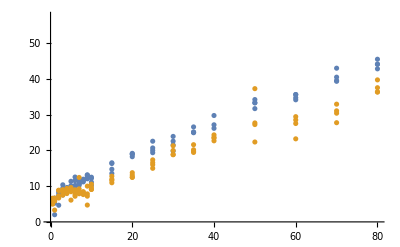

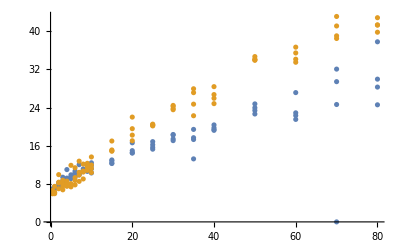

```mathematica
ListPlot[{rb87w11,rb85w11}]
ListPlot[{rb87w12,rb85w12}]
```